```mathematica
Clear["Global`*"]
SetDirectory[FileNameJoin[{NotebookDirectory[],"../figs/"}]]
```

/Users/marknovak/Git/aaaManuscripts/GeometricComplexity/figs

SC_2= -Log_ef(x|(Θ̂)_x)+k/2 Log_e(n/(2 π))+Log_e∫_Θ √(det I(Θ))ⅆΘ + o(1);
The first term is the likelihood. The second term is the parameter and sample size dependent component.
The third term containing I(Θ), the Expected Fisher Information Matrix, reflects the model's flexibility.

```mathematica
cm=72/2.54;
```

### Second Term dependence on k and n

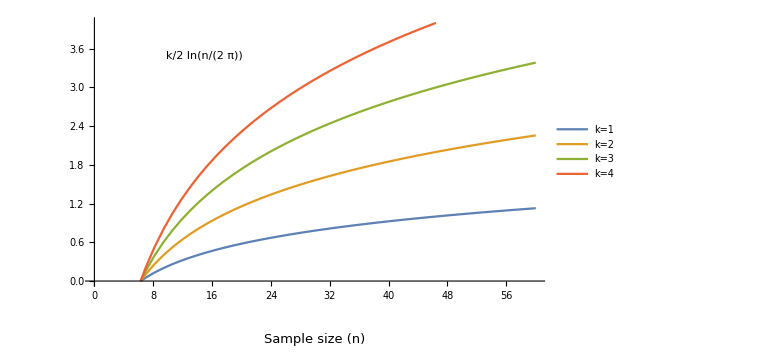

```mathematica
p1=
Plot[
Evaluate@Table[k/2 Log[n/(2 π)],{k,1,4}],{n,1,60},
PlotRange->{{0,60},{0,4}},
PlotLegends->Placed[{"k=1","k=2","k=3", "k=4"},Above],
PlotRangeClipping->False,
ImagePadding->{{50,5}, {30, 5}},
Epilog->{
Style[Text["k/2"ln[n/(2 π)],{15,3.5}],12],
Text[Style["Sample size (n)",13],Scaled[{0.5,-0.2}]],Rotate[Text[Style["Parametric\ncomplexity",13],Scaled[{-0.2,0.5}]],90 Degree]
},
ImageSize->Large
]
Export["ParamComp_2ndTerm.pdf",Show[p1,ImageSize-> 8 cm]];
```